```mathematica
a=({{1, 0, 0}, {((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h)))}, {(((10000)(1.5))/(2h)), (-((20000)(1.5))/h), (((30000)(1.5))/(2h))}})
```

{{1,0,0},{(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h},{7500./h,-30000./h,22500./h}}

```mathematica
b=({{0}, {-50}, {0}})
```

{{0},{-50},{0}}

```mathematica
LinearSolve[a,b]
```

{{0.},{(0.1 h^2)/(30.+1. h)},{(0.133333 h^2)/(30.+1. h)}}

```mathematica
(*let*)h=.1
```

0.1

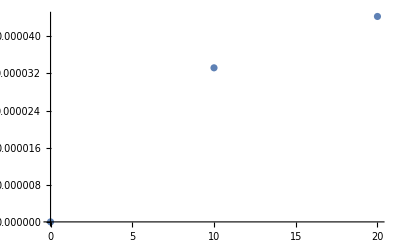

```mathematica
ListPlot[{{0,0},{10,0.00003322259136212626},{20,0.00004429678848283502}}]
```

```mathematica
(*makes logical sense*)
```